```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

# Complex Variables Toolkit - Final Project

## This package will contain many visualization tools that allows one to understand how complex functions behave

## Complex plane to image plane

### plotImage takes in a list of points, a complex function, and two plot ranges and outputs the original and its image.

```mathematica
getImagePts[expr_,pts_]:=Module[{imgPts},
imgPts={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@pts;
Return[imgPts]]
getImagePts::usage="getImagePts[expr,pts] takes in an expression and a list of points, returns the image points"

plotImage[pts_,expr_,pltRange1_:Automatic,PltRange2_:Automatic,colors_:1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1, Thick, Line[#2]}&,{colors,pts}], PlotRange -> pltRange1, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[MapThread[{#1, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #2]}&,{colors,pts}], PlotRange -> PltRange2, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
plotImage::usage="plotImage[pts,expr,pltRange1:Automatic,PltRange2:Automatic,colors:1] plotImage maps a list of points using an expression and plots both on the complex and image planes"
```

getImagePts[expr,pts] takes in an expression and a list of points, returns the image points

plotImage[pts,expr,pltRange1:Automatic,PltRange2:Automatic,colors:1] plotImage maps a list of points using an expression and plots both on the complex and image planes

```mathematica
Dimensions@gridPts
```

{}

### makeCirclePoints will make expanding circles given smallest radius, largest radius, and a step size

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,(largeRadius-smallRadius)/(numCircles-1)]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

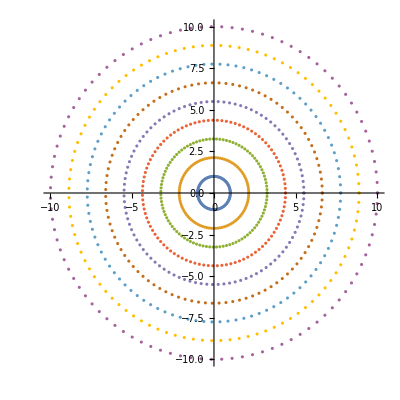

```mathematica
ListPlot[makeCirclePoints[1,10,9,100],AspectRatio->1]
```

```mathematica
makeSphereSpacedCirclePoints[numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,makeSphereSpacedPoints[numCircles]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

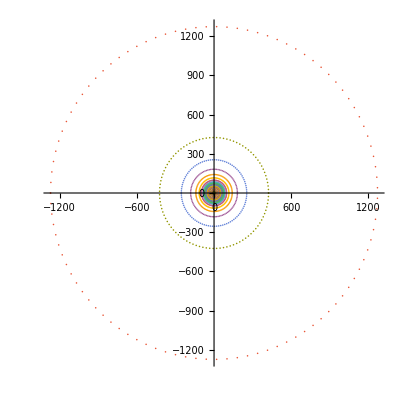

```mathematica
ListPlot[makeSphereSpacedCirclePoints[1000,100],AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[makeExponentialSpacedCirclePoints]
```

```mathematica
makeExponentialSpacedCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,fSpace[smallRadius,largeRadius,numCircles]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

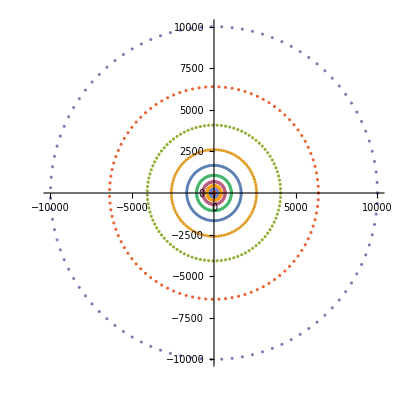

```mathematica
ListPlot[makeExponentialSpacedCirclePoints[2,10000,20,100],AspectRatio->1,PlotRange->Full]
```

{RGBColor[0.1822735662247359, 0.19779693397670184, 0.28588748050879853],RGBColor[0.6555931494777429, 0.8225258040898773, 0.5468156422733892],RGBColor[0.7061583909262095, 0.9895255759745891, 0.3476632262576922],RGBColor[0.6621827876329953, 0.7485352462242729, 0.9649164071933296],RGBColor[0.3578759760046484, 0.8655137220560811, 0.6506993906291605],RGBColor[0.4880743164533268, 0.6614537054092224, 0.8729347161261349],RGBColor[0.6736285881913768, 0.11061607384300975, 0.3007893443057963]}

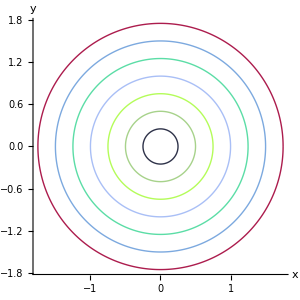
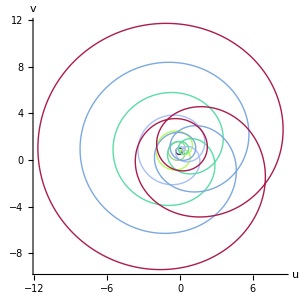

```mathematica
expr=(z+1)(z-.5)(z-1.5I);
pts=makeCirclePoints[.25,1.75,.25];
circleColors=makeRandomColors[pts]
n=2;
m=3;
plotImage[pts,expr,n,m,circleColors]
```

### makeGridPoints will make a grid of lines given user entered parameters

```mathematica
Clear[fSpace,makeVerticalPts,makeHorizontalPts,makeGridPts,makeLogVerticalPts,makeLogHorizontalPts,makeLogVerticalPts2,makeLogHorizontalPts2]
```

```mathematica
fSpace[min_,max_,numPts_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(numPts-1)]]]
fSpace::usage="fSpace[min, max, steps, Log] gives (default) log spaced points from min to max over a given number of points"
```

fSpace[min, max, steps, Log] gives (default) log spaced points from min to max over a given number of points

```mathematica
makeVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,Range[min,max,(max-min)/(ptsPerLine-1)]}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,Range[min,max,(max-min)/(ptsPerLine-1)]}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[min,max,ptsPerLine,numLines];
horiPts=makeHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]

makeLogVerticalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts},
vertPts=Table[Table[{x,y},{y,fSpace[min,max,ptsPerLine]}],{x,min,max,(max-min)/(numLines-1)}];
Return[Re[vertPts]]
]

makeLogHorizontalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,fSpace[min,max,ptsPerLine]}],{y,min,max,(max-min)/(numLines-1)}];
Return[Re[horiPts]]
]

makeLogGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertLogPts,horiLogPts,pts},
vertLogPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
horiLogPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiLogPts,vertLogPts];
Return[pts]
]

makeLogVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posVertPts,negVertPts},
posVertPts=Table[Table[{x,y},{y,fSpace[.001,max,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
negVertPts=Table[Table[{x,y},{y,fSpace[min,-.001,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negVertPts,posVertPts}];
Return[Re[pts]]
]

makeLogHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posHoriPts,negHoriPts},
posHoriPts=Table[Table[{x,y},{x,fSpace[.01,max,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
negHoriPts=Table[Table[{x,y},{x,fSpace[min,-.01,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negHoriPts,posHoriPts}];
Return[Re[pts]]
]
```

### old

```mathematica
makeVerticalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{vertPts},
newStep=stepSize+RandomReal[{.01,.02}];
vertPts=Table[Table[{x,y},{y,start,end,newStep}],{x,start,end,lineSpacing}];
Return[vertPts]
]

makeHorizontalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{horiPts},
newStep=stepSize+RandomReal[{.01,.02}];
horiPts=Table[Table[{x,y},{x,start,end,newStep}],{y,start,end,lineSpacing}];
Return[horiPts]
]
```

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]
```

### Equal space test constants

```mathematica
numPts=1000;
numLines=3;
min=-10;
max=10;
expr=z^3
```

z^3

#### first make vertical lines

{7,1,2}

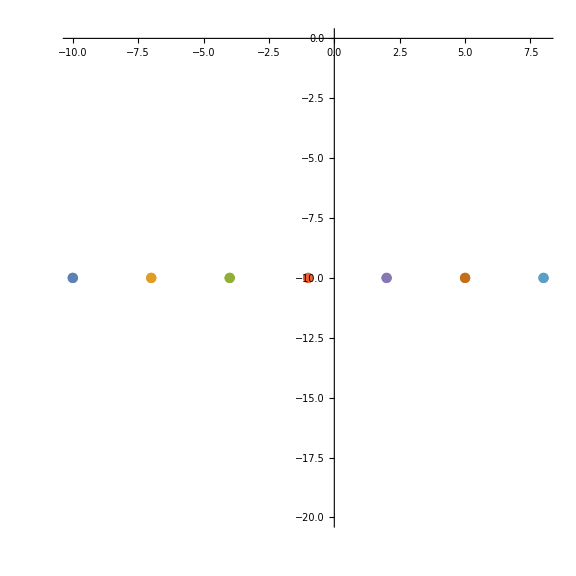

```mathematica
vertPts=makeVerticalPts[min,max,numPts,numLines];
Dimensions[vertPts]
ListPlot[vertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{7,1,2}

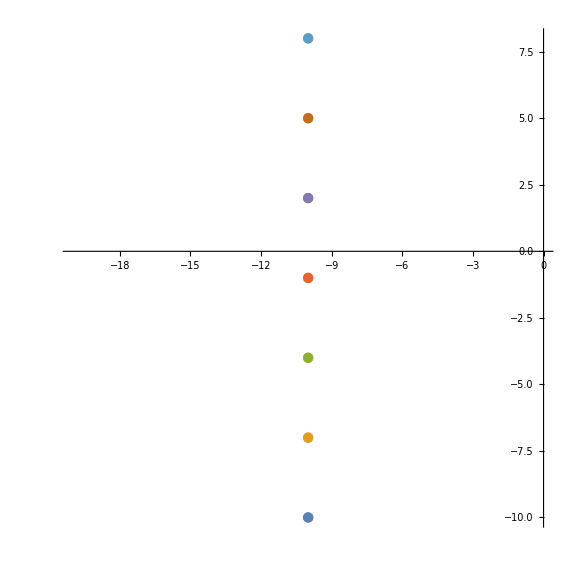

```mathematica
horiPts=makeHorizontalPts[min,max,numPts,numLines];
Dimensions[horiPts]
ListPlot[horiPts,ImageSize->Large,AspectRatio->1]
```

### Log test constants

```mathematica
ptsPerLine=100;
numLines=3;
min=-100;
max=100;
expr=z^3
```

z^3

{3,100,2}

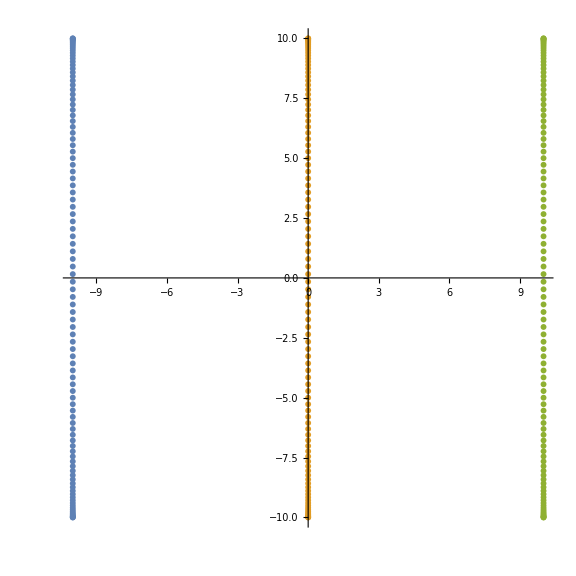

```mathematica
logVertPts=makeLogVerticalPts2[-10,10,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

```mathematica
Range[-10,10,20/(21-1)]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Log[0]
```

-∞

```mathematica
N@Re@Log[Range[-3,3,1/10]]
```

{1.09861,1.06471,1.02962,0.993252,0.955511,0.916291,0.875469,0.832909,0.788457,0.741937,0.693147,0.641854,0.587787,0.530628,0.470004,0.405465,0.336472,0.262364,0.182322,0.0953102,0.,-0.105361,-0.223144,-0.356675,-0.510826,-0.693147,-0.916291,-1.20397,-1.60944,-2.30259,-∞,-2.30259,-1.60944,-1.20397,-0.916291,-0.693147,-0.510826,-0.356675,-0.223144,-0.105361,0.,0.0953102,0.182322,0.262364,0.336472,0.405465,0.470004,0.530628,0.587787,0.641854,0.693147,0.741937,0.788457,0.832909,0.875469,0.916291,0.955511,0.993252,1.02962,1.06471,1.09861}

#### first make vertical lines

{3,100,2}

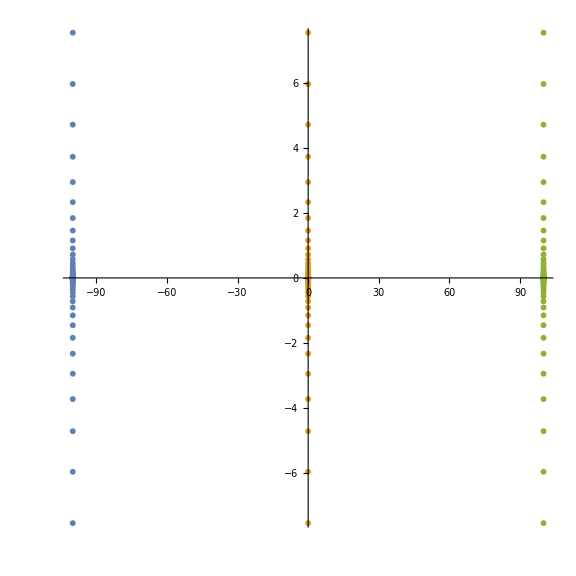

```mathematica
logVertPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{3,100,2}

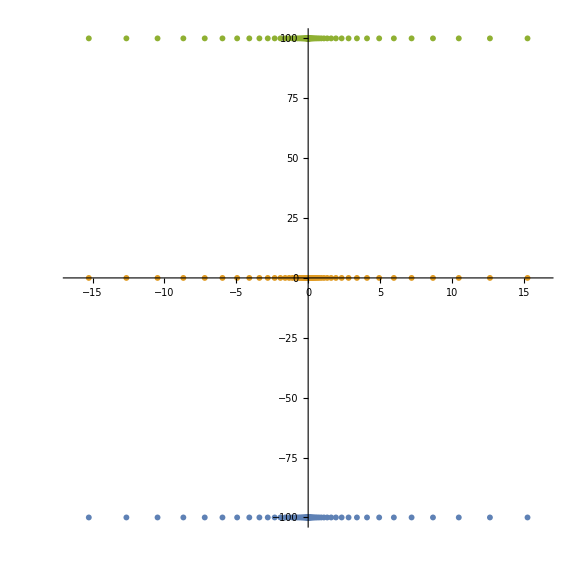

```mathematica
logHoriPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
Dimensions[logHoriPts]
ListPlot[logHoriPts,ImageSize->Large,AspectRatio->1]
```

### Next try to make a grid

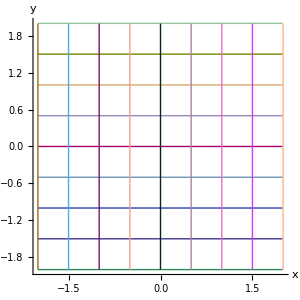
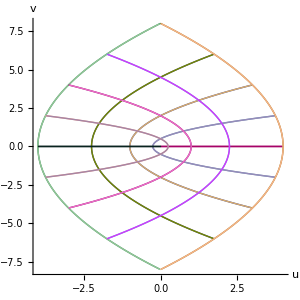

```mathematica
gridPts=makeGridPts[-2,2,.005,.5];
gridColors=makeRandomColors[gridPts];
plotImage[gridPts,z^2,Automatic,10,gridColors]
```

## Experiment with Riemann sphere stereographic projection

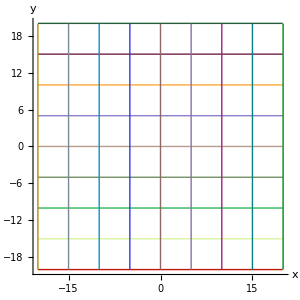
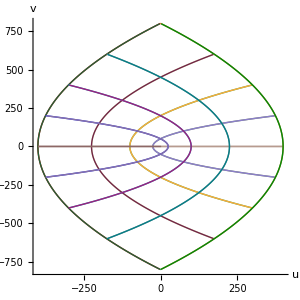

```mathematica
gridPts=makeGridPts[-20,20,.1,5];
gridColors=makeRandomColors[gridPts];
plotImage[gridPts,z^2,Automatic,10,gridColors]
```

```mathematica
gridPts[[1]][[1]]
```

{-20.,-20}

```mathematica
complexTo3D[point_]:=Module[{x,y,z,mix,X,Y,Z},
x=point[[1]];
y=point[[2]];
mix=(2x+ⅈ 2y)/(1+x^2+y^2);
X=Re[mix];
Y=Im[mix];
z=x+ⅈ y;
Z=(Abs[z]^2-1)/(Abs[z]^2+1);
Return[{X,Y,Z}]
]

complexPtsTo3D[points_]:=Module[{spherePts3D},
spherePts3D=complexTo3D[#]&/@#&/@points;
Return[spherePts3D]
]
```

```mathematica
complexTo3D[{1,1}]
```

{2/3,2/3,1/3}

```mathematica
pts3D=complexTo3D[#]&/@#&/@gridPts;
colors3D=makeRandomColors[pts3D]
```

{RGBColor[0.7417998814906672, 0.3069111995410654, 0.04311612400427389],RGBColor[0.6948046715673788, 0.26942223507281127, 0.7596909679259469],RGBColor[0.3336336692751125, 0.1415882384517524, 0.508806373643155],RGBColor[0.9675679196089755, 0.7520833176147121, 0.3503121266052103],RGBColor[0.49351293760669623, 0.9439738340687875, 0.6596699578711926],RGBColor[0.34153426271060394, 0.9394006264652699, 0.8713410962776347],RGBColor[0.5856204390877855, 0.9692593805428495, 0.6648417537587334],RGBColor[0.191983128947403, 0.6958641652375508, 0.6482991941147422],RGBColor[0.0032665068685417964, 0.4176101594061674, 0.19764474605796023],RGBColor[0.8343201397114268, 0.57758930087297, 0.11669594848349307],RGBColor[0.30183405498211435, 0.4140508311981219, 0.00746500116220572],RGBColor[0.5415755595161256, 0.7097572717960943, 0.17405413179178097],RGBColor[0.781850697675571, 0.7729279028628862, 0.28193222475523605],RGBColor[0.5731075653118842, 0.11749847809892922, 0.1361023908710859],RGBColor[0.8840561591104856, 0.622638756056807, 0.344133311014311],RGBColor[0.47208315160769776, 0.5113126252362368, 0.9471152162388377],RGBColor[0.6523677508491419, 0.1062215914144422, 0.9921419347110048],RGBColor[0.8650213916307752, 0.11334932817620791, 0.5364624971965457]}

```mathematica
ListPointPlot3D[pts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

### 1 to 100 log spaced

```mathematica
Re@fSpace[-20,20,100]
```

{-20.,-19.9899,-19.9597,-19.9094,-19.8391,-19.7488,-19.6386,-19.5086,-19.359,-19.1899,-19.0014,-18.7939,-18.5674,-18.3222,-18.0585,-17.7767,-17.477,-17.1597,-16.8251,-16.4735,-16.1054,-15.7211,-15.3209,-14.9053,-14.4747,-14.0295,-13.5702,-13.0972,-12.6111,-12.1122,-11.6011,-11.0784,-10.5445,-10.,-9.44542,-8.88133,-8.3083,-7.7269,-7.13772,-6.54136,-5.93841,-5.32948,-4.71518,-4.09613,-3.47296,-2.8463,-2.21676,-1.585,-0.951638,-0.317319,0.317319,0.951638,1.585,2.21676,2.8463,3.47296,4.09613,4.71518,5.32948,5.93841,6.54136,7.13772,7.7269,8.3083,8.88133,9.44542,10.,10.5445,11.0784,11.6011,12.1122,12.6111,13.0972,13.5702,14.0295,14.4747,14.9053,15.3209,15.7211,16.1054,16.4735,16.8251,17.1597,17.477,17.7767,18.0585,18.3222,18.5674,18.7939,19.0014,19.1899,19.359,19.5086,19.6386,19.7488,19.8391,19.9094,19.9597,19.9899,20.}

```mathematica
Range[-1,1,(1-(-1))/(20-1)]
```

{-1,-17/19,-15/19,-13/19,-11/19,-9/19,-7/19,-5/19,-3/19,-1/19,1/19,3/19,5/19,7/19,9/19,11/19,13/19,15/19,17/19,1}

## Log grid Riemann sphere

```mathematica
ptsPerLine=100;
numLines=5;
min=-10000;
max=10000;
expr=z^3
```

z^3

```mathematica
logGridPts=makeLogGridPts[min,max,ptsPerLine,numLines];
Dimensions[logGridPts]
```

{10,100,2}

```mathematica
logPts3D=pts3D=complexTo3D[#]&/@#&/@logGridPts;
Dimensions[logPts3D]
```

{10,100,3}

```mathematica
colors3D=makeRandomColors[logPts3D]
```

{RGBColor[0.39963706664833043, 0.3639996089168511, 0.5633120480437919],RGBColor[0.8829486375840077, 0.3176966648375399, 0.7603036580544369],RGBColor[0.21495925775555969, 0.8531927674713622, 0.8751453905866018],RGBColor[0.6525649087623231, 0.5551810263136963, 0.35584557613986045],RGBColor[0.3544325297163011, 0.02054265311351222, 0.45080471067005745],RGBColor[0.5621690207073677, 0.6220431288893649, 0.23384003562848044],RGBColor[0.6921433773149694, 0.5037646568254865, 0.4951359968128195],RGBColor[0.5055979019708186, 0.8191720292120539, 0.5641189597591441],RGBColor[0.5371638324866654, 0.5064879027805564, 0.9176693985793878],RGBColor[0.7340427431349259, 0.7374414213789124, 0.6774569575704001]}

```mathematica
ListPointPlot3D[logPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

## Trying to get circular spaced points

```mathematica
Clear[makeRiemannUnitCirclePts]
```

```mathematica
makeRiemannUnitCirclePts[numPts_]:=Module[
{angles, pts},
angles=N@Range[0Pi,2Pi,(2 Pi - 0Pi)/(numPts - 1)];
pts=Table[{Cos[ang],0,Sin[ang]},{ang,angles}];
Return[pts]
]
```

```mathematica
riemannPointToComplexPlane[{X_,Y_,Z_}]:=Module[{sol,pair},
sol=Solve[{x+ⅈ y==(X+ⅈ Y)/(1-Z)},{x∈Reals,y∈Reals}];
pair=({x,y}/.sol)[[1]];
Return[pair]
]
```

```mathematica
makeSphereSpacedPoints[numPts_]:=Module[{pts,complexPts,realPts},
pts=makeRiemannUnitCirclePts[numPts];
complexPts=riemannPointToComplexPlane[#]&/@pts;
realPts=complexPts[[All,1]];
Return[realPts]
]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

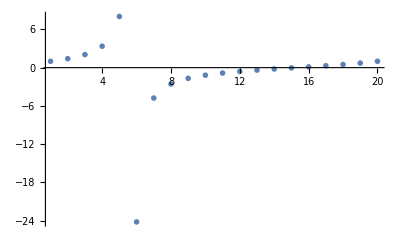

```mathematica
sphericalPts=makeSphereSpacedPoints[20]
ListPlot[sphericalPts,PlotStyle->PointSize[.01],PlotRange->All]
```

```mathematica
makeSphereSpacedPoints[20]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

```mathematica
horiPts=Table[Table[{x,y},{x,{1.,1.4005871438998048,2.045532694709038,3.3589407898715407,8.022471262465187,-24.177770864938736,-4.769218689284606,-2.5627803610641804,-1.67821653689189,-1.1806977689241733,-0.8469567964977006,-0.5958706627048448,-0.3902012108383555,-0.20967795044642917,-0.04136030594326412,0.12464987000685275,0.2977128989636771,0.4888702109658738,0.7139862766522278,0.9999999999999998}}],{y,-1,1,(1-(-1))/(2-1)}]
```

{{{1.,-1},{1.40059,-1},{2.04553,-1},{3.35894,-1},{8.02247,-1},{-24.1778,-1},{-4.76922,-1},{-2.56278,-1},{-1.67822,-1},{-1.1807,-1},{-0.846957,-1},{-0.595871,-1},{-0.390201,-1},{-0.209678,-1},{-0.0413603,-1},{0.12465,-1},{0.297713,-1},{0.48887,-1},{0.713986,-1},{1.,-1}},{{1.,1},{1.40059,1},{2.04553,1},{3.35894,1},{8.02247,1},{-24.1778,1},{-4.76922,1},{-2.56278,1},{-1.67822,1},{-1.1807,1},{-0.846957,1},{-0.595871,1},{-0.390201,1},{-0.209678,1},{-0.0413603,1},{0.12465,1},{0.297713,1},{0.48887,1},{0.713986,1},{1.,1}}}

```mathematica
Clear[makeHorizontalLines]
```

```mathematica
makeHorizontalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{x,spherePts}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeVerticalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{y,spherePts}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeGrid[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
horiPts=makeVerticalLines[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
makeGrid::usage="makeGrid[min,max,ptsPerLine,numLines] makes a grid of sphere spaced points given line bounds of min, max, ptsPerLine, and numLines"
```

makeGrid[min,max,ptsPerLine,numLines] makes a grid of sphere spaced points given line bounds of min, max, ptsPerLine, and numLines

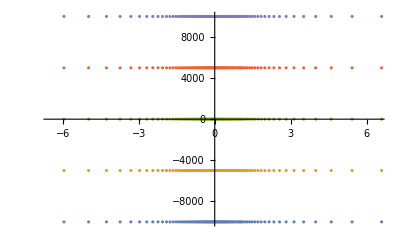

```mathematica
horiPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
ListPlot[horiPts]
```

```mathematica
horiPts//Dimensions
```

{5,100,2}

```mathematica
expr=1/z;
image={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@horiPts;
Dimensions[image]
```

{5,100,2}

```mathematica
min=-3;
max=3;
ptsPerLine=200;
numLines=3;
```

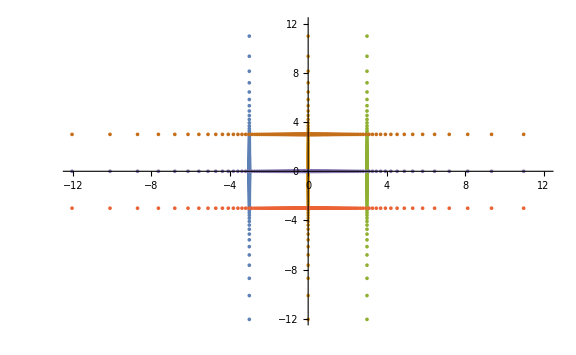

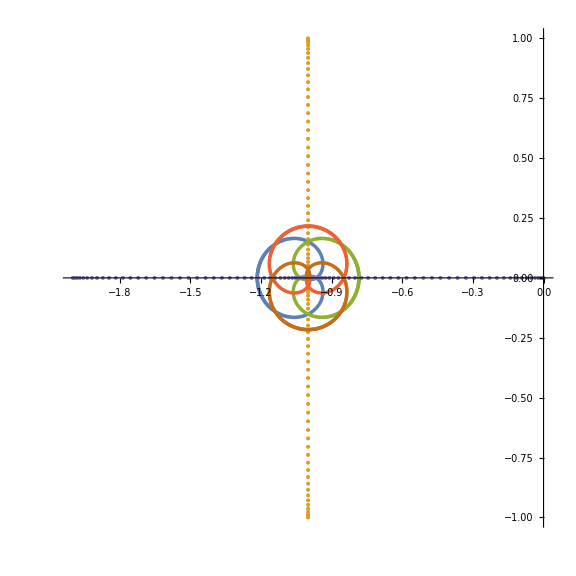

```mathematica
expr=(z^3-1);
gridPts=makeGrid[min,max,ptsPerLine,numLines];
ListPlot[gridPts]
spherePts3D=complexTo3D[#]&/@#&/@gridPts;
image=getImagePts[expr,spherePts3D];
ListPlot[image,PlotRange->Full,ImageSize->Large,AspectRatio->1]
```

```mathematica
Graphics3D[Join[cylinders[complexPtsTo3D[image],.03],{Opacity[.3],Sphere[{0,0,0}]}]]
```

-Graphics3D-

```mathematica
takingPts[takes_,pts_]:=Module[{newPts},
newPts=Take[pts,#]&/@takes;
Return[newPts]]

cylinderPts[pts_]:=Module[{takes,returnPts},
takes=Table[{x,x+1},{x,1,Dimensions[pts][[2]]-1}];
returnPts=takingPts[takes,#]&/@pts
]

cylinders[pts_,radius_]:=Module[{},
Return[Cylinder[#,radius]&/@#&/@cylinderPts[pts]]]
```

```mathematica
Export["grid.stl",Graphics3D[cylinders[spherePts3D,.05],{"STL,","BinaryFormat"->True}]]
```

grid.stl

```mathematica
Import["grid.stl"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
Export["grid_10_7.stl",Graphics3D[cylinders[complexPtsTo3D[makeGrid[-1,1,100,12]],.01]],{"STL,","BinaryFormat"->True}]
```

grid_10_7.stl

```mathematica
grid107=Import["grid_10_7.stl"]
```

Import::nffil: File not found during Import.

$Failed

## Newtons method

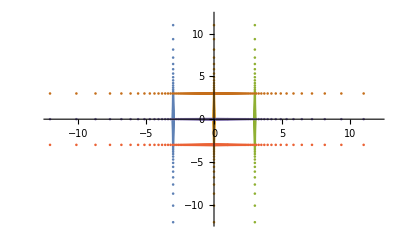

```mathematica
expr=(z-z/3+1/(3 z^2));
gridPts=makeGrid[min,max,ptsPerLine,numLines];
ListPlot[gridPts]
```

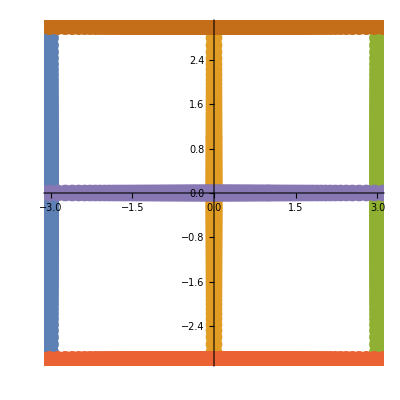
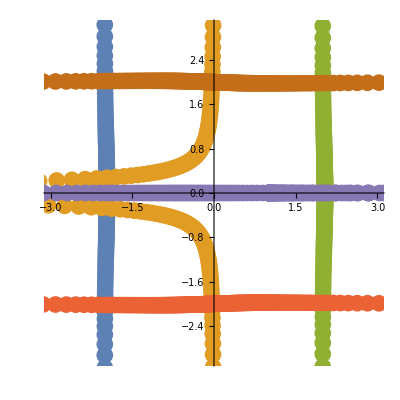
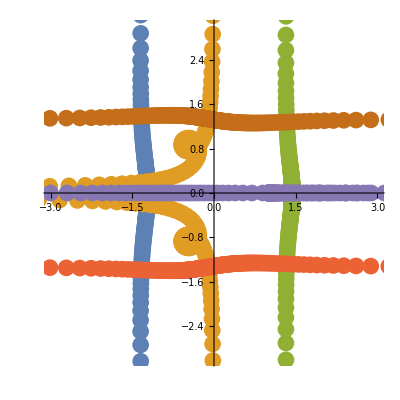
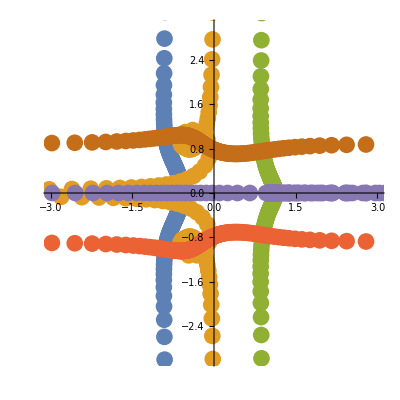
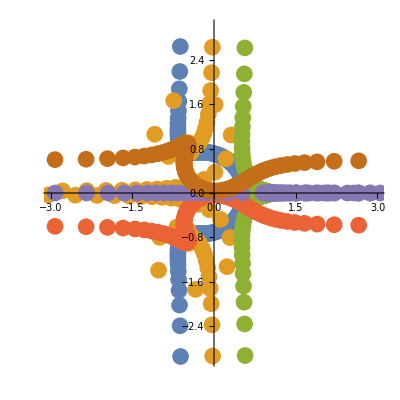
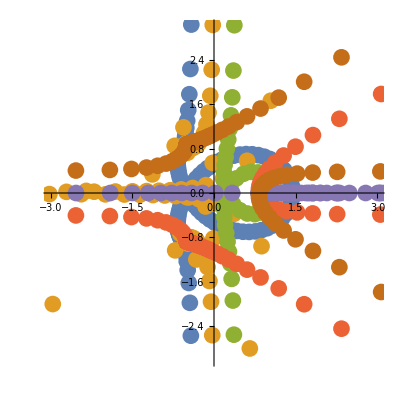
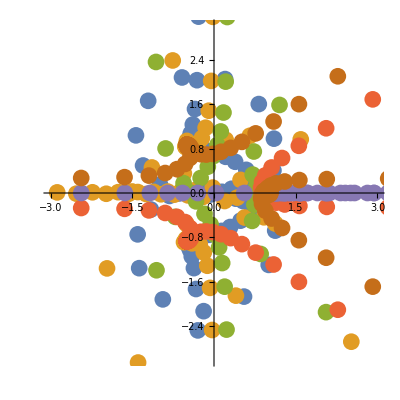
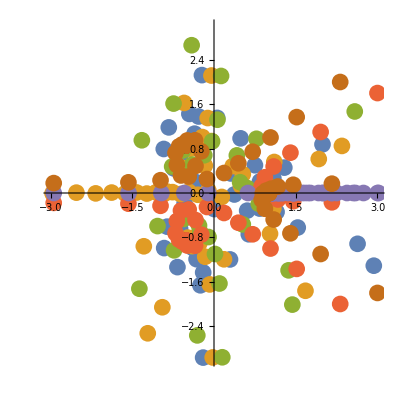
0
-Graphics-
{1,-Graphics-}
{2,-Graphics-}
{3,-Graphics-}
{4,-Graphics-}
{5,-Graphics-}
{6,-Graphics-}
{7,-Graphics-}
{8,-Graphics-}
{9,-Graphics-}
{10,-Graphics-}
{11,-Graphics-}
{12,-Graphics-}
{13,-Graphics-}
{14,-Graphics-}
{15,-Graphics-}
{16,-Graphics-}
{17,-Graphics-}
{18,-Graphics-}
{19,-Graphics-}
{20,-Graphics-}
{21,-Graphics-}
{22,-Graphics-}
{23,-Graphics-}
{24,-Graphics-}
{25,-Graphics-}
{26,-Graphics-}
{27,-Graphics-}
{28,-Graphics-}
{29,-Graphics-}
{30,-Graphics-}
{31,-Graphics-}
{32,-Graphics-}
{33,-Graphics-}
{34,-Graphics-}
{35,-Graphics-}
{36,-Graphics-}
{37,-Graphics-}
{38,-Graphics-}
{39,-Graphics-}
{40,-Graphics-}

```mathematica
imagePtsN=gridPts;

Column[Join[{0,ListPlot[gridPts,PlotRange->{{-3,3},{-3,3}},PlotStyle->PointSize[.03],AspectRatio->1]},Table[imagePtsN=getImagePts[expr,imagePtsN];{n,ListPlot[imagePtsN,PlotRange->{{-3,3},{-3,3}},PlotStyle->PointSize[.03],AspectRatio->1]}
,{n,1,40}]]]
```